```mathematica
dataWeek3={{1,27},{2,43},{3,54},{4,64},{5,75},{6,82},{7,84},{8,89},{9,92},{10,93},{11,97},{12,104},{13,106},{14,111},{15,116},{16,122},{17,122},{18,127},{19,128},{20,129},{21,131},{22,132},{23,134},{24,135},{25,136}}
```

{{1,27},{2,43},{3,54},{4,64},{5,75},{6,82},{7,84},{8,89},{9,92},{10,93},{11,97},{12,104},{13,106},{14,111},{15,116},{16,122},{17,122},{18,127},{19,128},{20,129},{21,131},{22,132},{23,134},{24,135},{25,136}}

```mathematica
(**transpose matrix)- next week)
```

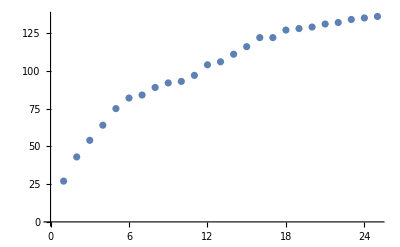

```mathematica
ListPlot[dataWeek3]
```

```mathematica
shortGoel=NonlinearModelFit[dataWeek3,a*(1-Exp[-b*t]),{a,b},t]
```

FittedModel[135.974 (1-ⅇ^(-0.138257 t))]

```mathematica
shortGoel["Function"]
```

135.974 (1-ⅇ^(-0.138257 #1))&

```mathematica
shortGoel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 135.974 | 3.00942 | 45.1829 | 5.72939×10^-24
b | 0.138257 | 0.00896322 | 15.425 | 1.27229×10^-13

```mathematica
shortGoel["BestFitParameters"]
```

{a→135.974,b→0.138257}

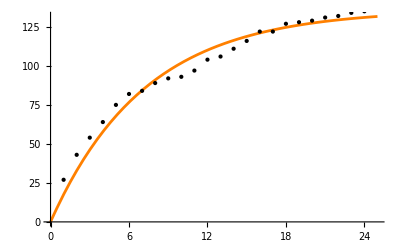

```mathematica
Plot[shortGoel[t],{t,0,25},Epilog->Point[dataWeek3],PlotStyle->Orange]
```

```mathematica
shortGoel["AIC"]
```

162.592

```mathematica
shortGoel["BIC"]
```

166.249

```mathematica
shortGoel["RSquared"]
```

0.997259

```mathematica
shortGoel["AdjustedRSquared"]
```

0.99702

```mathematica
generalGoel=NonlinearModelFit[dataWeek3,a*(1-Exp[-b*t^c]),{{a,160},b,c},t]
```

FittedModel[190.443 (1-ⅇ^(-0.167696 t^0.633089))]

```mathematica
generalGoel["Function"]
```

190.443 (1-ⅇ^(-0.167696 #1^0.633089))&

```mathematica
generalGoel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 190.443 | 19.068 | 9.98756 | 1.2348×10^-9
b | 0.167696 | 0.0124867 | 13.43 | 4.44399×10^-12
c | 0.633089 | 0.0410005 | 15.441 | 2.73814×10^-13

```mathematica
generalGoel["BestFitParameters"]
```

{a→190.443,b→0.167696,c→0.633089}

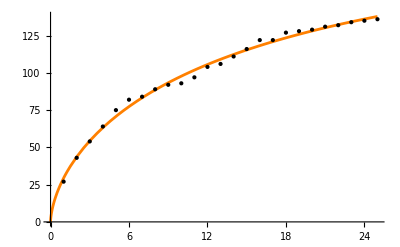

```mathematica
Plot[generalGoel[t],{t,0,25},Epilog->Point[dataWeek3],PlotStyle->Orange]
```

```mathematica
generalGoel["AIC"]
```

123.546

```mathematica
generalGoel["BIC"]
```

128.422

```mathematica
generalGoel["RSquared"]
```

0.999472

```mathematica
generalGoel["AdjustedRSquared"]
```

0.999399

```mathematica
delayedSshapedModel = NonlinearModelFit[dataWeek3,a (1-(1+b*t) Exp[-b*t]),{{a,160},b},t]
```

FittedModel[124.672 (1-ⅇ^(-0.355907 t) (1+0.355907 t))]

```mathematica
delayedSshapedModel["Function"]
```

124.672 (1-ⅇ^(-0.355907 #1) (1+0.355907 #1))&

```mathematica
delayedSshapedModel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 124.672 | 3.52272 | 35.391 | 1.46032×10^-21
b | 0.355907 | 0.0292121 | 12.1835 | 1.63157×10^-11

```mathematica
delayedSshapedModel["BestFitParameters"]
```

{a→124.672,b→0.355907}

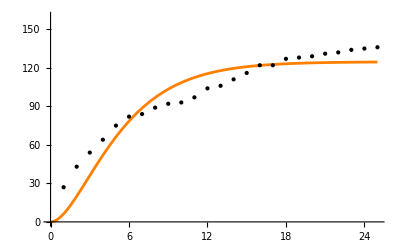

```mathematica
Plot[delayedSshapedModel[t],{t,0,25},Epilog->Point[dataWeek3],PlotStyle->Orange,PlotRange->{0,160}]
```

```mathematica
delayedSshapedModel["AIC"]
```

197.436

```mathematica
delayedSshapedModel["BIC"]
```

201.093

```mathematica
delayedSshapedModel["RSquared"]
```

0.988952

```mathematica
delayedSshapedModel["AdjustedRSquared"]
```

0.987991

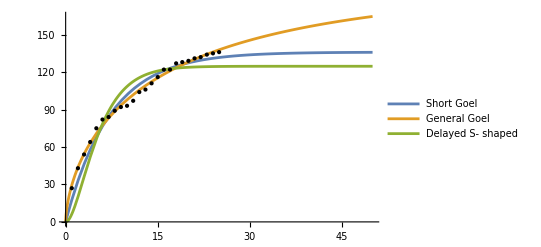

```mathematica
Plot[{shortGoel[t],generalGoel[t],delayedSshapedModel[t]},{t,0,50},PlotLegends->{"Short Goel","General Goel","Delayed S- shaped"},PlotStyle->{"red","green","blue"}, Epilog->Point[dataWeek3]]
```

```mathematica
Grid[{#,shortGoel[#],generalGoel[#],delayedSshapedModel[#]}&[{"AIC","BIC","RSquared","AdjustedRSquared"}],Frame->All]
```

AIC | BIC | RSquared | AdjustedRSquared
162.592 | 166.249 | 0.997259 | 0.99702
123.546 | 128.422 | 0.999472 | 0.999399
197.436 | 201.093 | 0.988952 | 0.987991

```mathematica
prediction=Table[{i,Round[generalGoel[i]]},{i,26,50}]
```

{{26,140},{27,141},{28,143},{29,144},{30,146},{31,147},{32,148},{33,149},{34,151},{35,152},{36,153},{37,154},{38,155},{39,156},{40,157},{41,158},{42,159},{43,159},{44,160},{45,161},{46,162},{47,162},{48,163},{49,164},{50,165}}

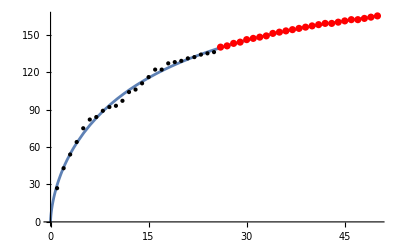

```mathematica
Show[Plot[generalGoel[t],{t,0,50},Epilog->Point[dataWeek3]],ListPlot[prediction,PlotStyle->Red]]
```

```mathematica
prediction=Table[{i,Round[generalGoel[i]]},{i,50,150}]
```

{{50,165},{51,165},{52,166},{53,166},{54,167},{55,168},{56,168},{57,169},{58,169},{59,170},{60,170},{61,171},{62,171},{63,172},{64,172},{65,172},{66,173},{67,173},{68,174},{69,174},{70,174},{71,175},{72,175},{73,175},{74,176},{75,176},{76,176},{77,177},{78,177},{79,177},{80,177},{81,178},{82,178},{83,178},{84,179},{85,179},{86,179},{87,179},{88,179},{89,180},{90,180},{91,180},{92,180},{93,181},{94,181},{95,181},{96,181},{97,181},{98,181},{99,182},{100,182},{101,182},{102,182},{103,182},{104,182},{105,183},{106,183},{107,183},{108,183},{109,183},{110,183},{111,183},{112,184},{113,184},{114,184},{115,184},{116,184},{117,184},{118,184},{119,184},{120,185},{121,185},{122,185},{123,185},{124,185},{125,185},{126,185},{127,185},{128,185},{129,185},{130,186},{131,186},{132,186},{133,186},{134,186},{135,186},{136,186},{137,186},{138,186},{139,186},{140,186},{141,186},{142,186},{143,187},{144,187},{145,187},{146,187},{147,187},{148,187},{149,187},{150,187}}

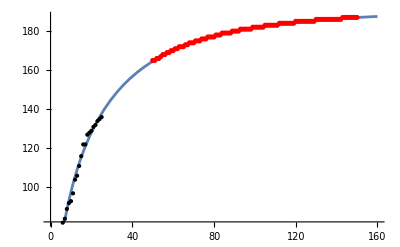

```mathematica
Show[Plot[generalGoel[t],{t,0,160},Epilog->Point[dataWeek3]],ListPlot[prediction,PlotStyle->Red]]
```

```mathematica
/** week 4/
```

a (1-ⅇ^(-((-1+ⅇ^(t β)) α)/β-t λ))

FittedModel[140.65 ⅇ^(-1.50002 ⅇ^(-0.141582«1»«1»))]

140.65 ⅇ^(-1.50002 ⅇ^(-0.141582 #1))&

| Estimate | Standard Error | t-Statistic | P-Value
a | 140.65 | 3.34768 | 42.0141 | 1.66356×10^-22
α | 1.50002 | 0.0733906 | 20.4388 | 8.46133×10^-16
β | 0.141582 | 0.0119094 | 11.8882 | 4.75715×10^-11

{a→140.65,α→1.50002,β→0.141582}

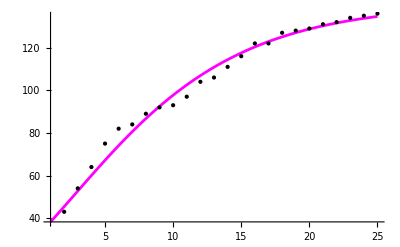

148.691

153.566

0.998555

0.998358

FittedModel[168.029 (1-ⅇ^(0.293737 (-1+ⅇ^(-«19» t))-0.0573606 t))]

168.029 (1-ⅇ^(0.293737 (-1+ⅇ^(-0.506395 #1))-0.0573606 #1))&

| Estimate | Standard Error | t-Statistic | P-Value
a | 168.029 | 12.5901 | 13.3461 | 1.0007×10^-11
α | 0.148747 | 0.0227301 | 6.54404 | 1.75547×10^-6
λ | 0.0573606 | 0.0139226 | 4.11997 | 0.00048773
β | -0.506395 | 0.142642 | -3.55011 | 0.00189446

```mathematica
Gompertz=a*Exp[-α*Exp[-β*t]];
GompertzMakeham=a*(1-Exp[-λ*t-(α/β)*(Exp[β*t]-1)])
gompertz=NonlinearModelFit[dataWeek3,Gompertz,{{a,139},{α,0.3},{β,0.5}},t]
gompertz["Function"]
gompertz["ParameterTable"]
gompertz["BestFitParameters"]
Plot[gompertz[t],{t,1,25},Epilog->Point[dataWeek3],PlotStyle->Magenta]
gompertz["AIC"]
gompertz["BIC"]
gompertz["RSquared"]
gompertz["AdjustedRSquared"]
gm=NonlinearModelFit[dataWeek3,GompertzMakeham,{{a,160},α,{λ,0.2},{β,-0.75}},t]
gm["Function"]
gm["ParameterTable"]
/** β e незначим параметър за модела/
gm["BestFitParameters"]
Plot[gm[t],{t,1,26},Epilog->Point[dataWeek3],PlotStyle->Orange]
Grid[{#,generalGoel[#],gompertz[#],gm[#]}&[{"AIC","BIC","RSquared","AdjustedRSquared"}],Frame->All]
Plot[{generalGoel[t],gompertz[t],gm[t]},{t,0,50},PlotLegends->{"General Goel","Gompertz","Gompertz Makeham"},PlotStyle->{"red","green","blue"}, Epilog->Point[dataWeek3]]
```

{a→168.029,α→0.148747,λ→0.0573606,β→-0.506395}

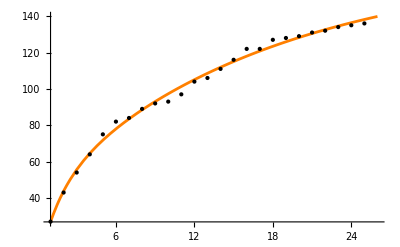

AIC | BIC | RSquared | AdjustedRSquared
123.546 | 128.422 | 0.999472 | 0.999399
148.691 | 153.566 | 0.998555 | 0.998358
120.739 | 126.833 | 0.999567 | 0.999484

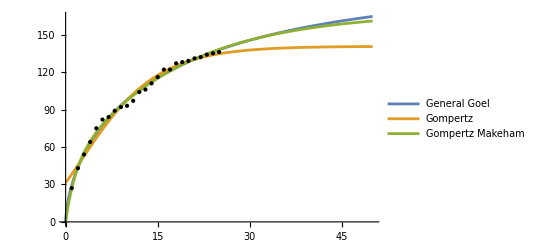

```mathematica
gm["BestFitParameters"]
Plot[gm[t],{t,1,26},Epilog->Point[dataWeek3],PlotStyle->Orange]
Grid[{#,generalGoel[#],gompertz[#],gm[#]}&[{"AIC","BIC","RSquared","AdjustedRSquared"}],Frame->All]
Plot[{generalGoel[t],gompertz[t],gm[t]},{t,0,50},PlotLegends->{"General Goel","Gompertz","Gompertz Makeham"},PlotStyle->{"red","green","blue"}, Epilog->Point[dataWeek3]]
```

```mathematica
prediction= Table[{i,Round[gm[i]]},{i,26,50}]
```

{{26,140},{27,141},{28,143},{29,144},{30,146},{31,147},{32,148},{33,149},{34,150},{35,151},{36,152},{37,153},{38,154},{39,155},{40,155},{41,156},{42,157},{43,157},{44,158},{45,159},{46,159},{47,160},{48,160},{49,160},{50,161}}

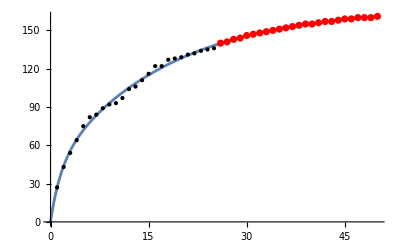

```mathematica
Show[Plot[gm[t],{t,0,50},Epilog->Point[dataWeek3]],ListPlot[prediction,PlotStyle->Red]]
```

```mathematica
modelPham=NonlinearModelFit[dataWeek3,a*(1-(β/(β-1+a^{t^b}))^α),{{a,139},{b,0.4},{β,5},α},t]
```

FittedModel[368.987 (1-1.10791 (1/(29.9052+«1»))^0.0298675)]

```mathematica
modelPham["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 368.987 | 851.293 | 0.433443 | 0.669113
b | 0.365975 | 0.429657 | 0.851785 | 0.403943
β | 30.9052 | 161.476 | 0.191392 | 0.850057
α | 0.0298675 | 0.0426733 | 0.69991 | 0.491665

```mathematica
modelPham["BestFitParameters"]
```

{a→368.987,b→0.365975,β→30.9052,α→0.0298675}

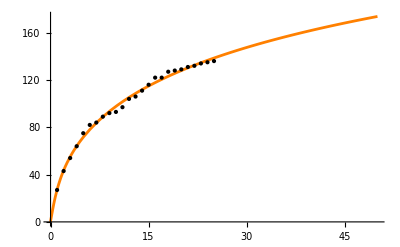

```mathematica
Plot[modelPham[t],{t,0,50},Epilog->Point[dataWeek3],PlotStyle->Orange]
```

```mathematica
modelPham["AIC"]
```

123.822

```mathematica
modelPham["BIC"]
```

129.916

```mathematica
modelPham["RSquared"]
```

0.99951

```mathematica
modelPham["AdjustedRSquared"]
```

0.999417

```mathematica
Zhang=NonlinearModelFit[dataWeek3,((1-(((1+α)*Exp[-b*t]))/(1+α*Exp[-b*t]))^{(c/b)*(p-β)})*(a/(p-β)),{{a,140},{b,0.5},{p,1.2},{c,0.3},{α,0.4},{β,-0.7}},t,MaxIterations->Infinity]
```

FittedModel[213.451 (1-(0.000784112 ⅇ^(«1»))/(1-0.999216 ⅇ^(«1»)))^0.59109]

```mathematica
Zhang["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 68.2146 | 0.829269 | 82.2587 | 1.01282×10^-25
b | 0.0000285842 | 136.721 | 2.0907×10^-7 | 1.
p | 0.40979 | 177.051 | 0.00231453 | 0.998177
c | 0.000052869 | 252.819 | 2.09118×10^-7 | 1.
α | -0.999216 | 3749.01 | -0.000266528 | 0.99979
β | 0.0902104 | 177.051 | 0.000509518 | 0.999599

```mathematica
Zhang["BestFitParameters"]
```

{a→68.2146,b→0.0000285842,p→0.40979,c→0.000052869,α→-0.999216,β→0.0902104}

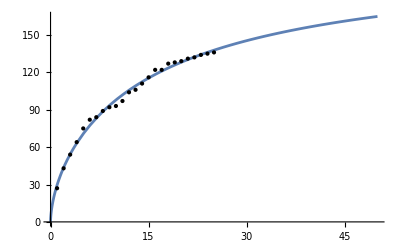

```mathematica
Plot[Zhang[t],{t,0,50},Epilog->Point[dataWeek3]]
```

```mathematica
chang=NonlinearModelFit[dataWeek3,a*(1-(β/(β+(α*t)^b))^α),{{a,160},{α,0.25},{b,-0.75},{β,0.7}},t,MaxIterations->Infinity]
```

FittedModel[1.06651×10^7 (1-0.999944 (1/(«23»+«24» t^(«19»)))^(6.09983×10^-6))]

```mathematica
chang["ParameterTable"]
```

General::munfl: Exp[-960.263] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.06651×10^7 | 3.50231×10^-14 | 3.04518×10^20 | 0.
α | 6.09983×10^-6 | 1.64719×10^-6 | 3.70317 | 0.00131813
b | 0.813294 | 0.118775 | 6.84736 | 9.06787×10^-7
β | 0.000106679 | 0.000202661 | 0.526393 | 0.604131

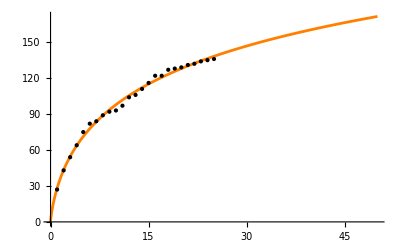

```mathematica
Plot[chang[t],{t,0,50},Epilog->Point[dataWeek3],PlotStyle->Orange]
```

```mathematica
yamadaExp=NonlinearModelFit[dataWeek3,a*(1-Exp[-r*α*(1-Exp[-β*t])]),{{a,160},{r,1.75},{α,0.2},{β,0.2}},t,MaxIterations->Infinity]
```

FittedModel[174.361 (1-ⅇ^(-1.7586 (1-ⅇ^(-«19» t))))]

```mathematica
yamadaExp["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 174.361 | 754.243 | 0.231174 | 0.819417
r | 3.92272 | 0.65998 | 5.9437 | 6.71531×10^-6
α | 0.448311 | 5.77482 | 0.077632 | 0.938856
β | 0.0682528 | 0.601796 | 0.113415 | 0.910779

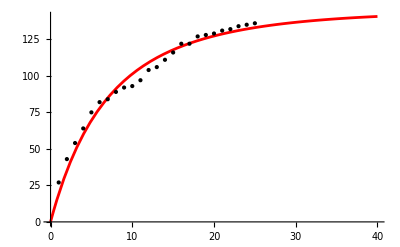

```mathematica
Plot[yamadaExp[t],{t,0,40},Epilog->Point[dataWeek3],PlotStyle->Red]
```

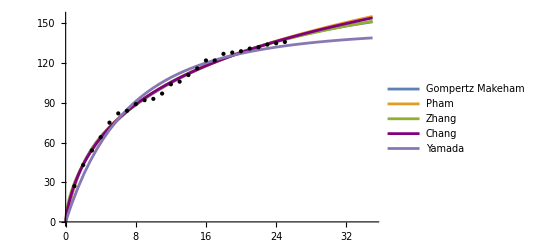

```mathematica
Plot[{gm[t],modelPham[t],Zhang[t],chang[t],yamadaExp[t]},{t,0,35},PlotStyle->{"blue","green","yellow",Purple,"red"},PlotLegends->{"Gompertz Makeham","Pham","Zhang","Chang","Yamada"},Epilog->Point[dataWeek3]]
```

```mathematica
Grid[{#,gm[#],modelPham[#],Zhang[#],chang[#],yamadaExp[#]}&[{"AIC","BIC","RSquared","AdjustedRSquared"}],Frame->All]
```

AIC | BIC | RSquared | AdjustedRSquared
120.739 | 126.833 | 0.999567 | 0.999484
123.822 | 129.916 | 0.99951 | 0.999417
130.639 | 139.171 | 0.999462 | 0.999293
124.549 | 130.644 | 0.999496 | 0.999399
157.826 | 163.92 | 0.99809 | 0.997727

Най- добри стойности получаваме за Gompertz Makeham.

```mathematica
INVERTEDEXPONENTIAL=a*(1-(1-Exp[-θ/t])^ϕ);
invertedExponential=NonlinearModelFit[dataWeek3,INVERTEDEXPONENTIAL,{{a,140},{θ,0.5},{ϕ,-0.75}},t,PrecisionGoal->Infinity]
```

FittedModel[-96.5122 (1-1/((1-ⅇ^(-«20»/t))^0.212309))]

```mathematica
invertedExponential["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -96.5122 | 44.5331 | -2.1672 | 0.041318
θ | 0.378833 | 0.126132 | 3.00347 | 0.00654179
ϕ | -0.212309 | 0.0494127 | -4.29664 | 0.000292339

standard error <estimate, t>2,p<0.05

```mathematica
invertedExponential["BestFitParameters"]
```

{a→-96.5122,θ→0.378833,ϕ→-0.212309}

General::munfl: Exp[-713.241] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

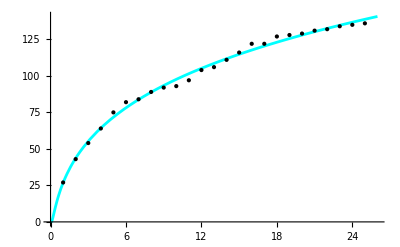

```mathematica
Plot[invertedExponential[t],{t,0,26},Epilog->Point[dataWeek3],PlotStyle->Cyan]
```

```mathematica
invertedExponential["AIC"]
```

121.724

```mathematica
invertedExponential["BIC"]
```

126.599

```mathematica
invertedExponential["RSquared"]
```

0.999509

```mathematica
invertedExponential["AdjustedRSquared"]
```

0.999442

```mathematica
TIESRM=a*Exp[-θ/t]*(1+λ-λ*Exp[-θ/t]);
tiesrm=NonlinearModelFit[dataWeek3,TIESRM,{{a,160},θ,λ},t]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[149.334 ⅇ^(-2.42498/t) (0.50063+0.49937 ⅇ^(-2.42498/t))]

```mathematica
tiesrm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 149.334 | 6.65827 | 22.4284 | 1.19921×10^-16
θ | 2.42498 | 7.53212 | 0.321952 | 0.750529
λ | -0.49937 | 4.30894 | -0.115892 | 0.90879

```mathematica
tiesrm["BestFitParameters"]
```

{a→149.334,θ→2.42498,λ→-0.49937}

General::munfl: Exp[-4565.59] is too small to represent as a normalized machine number; precision may be lost.

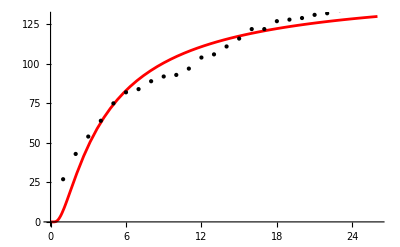

```mathematica
Plot[tiesrm[t],{t,0,26},Epilog->Point[dataWeek3],PlotStyle->Red]
```

```mathematica
tiesrm["AIC"]
```

180.116

```mathematica
tiesrm["BIC"]
```

184.992

```mathematica
tiesrm["RSquared"]
```

0.994922

```mathematica
tiesrm["AdjustedRSquared"]
```

0.994229

```mathematica
PhamLog=a*(1-β/(β+Log[(a+Exp[b*t])/(a+1)]))^α;
phamLog=NonlinearModelFit[dataWeek3,PhamLog,{{a,160},b,β,α},t]
```

FittedModel[208.526 (1-168.62/(168.62+Log[«1»]))^0.163056]

```mathematica
phamLog["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 208.526 | 397.848 | 0.524134 | 0.605674
b | 0.703828 | 0.307645 | 2.28779 | 0.0326248
β | 168.62 | 2346. | 0.0718757 | 0.943381
α | 0.163056 | 0.0587031 | 2.77764 | 0.0112807

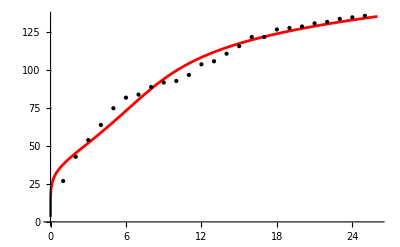

```mathematica
Plot[phamLog[t],{t,0,26},Epilog->Point[dataWeek3],PlotStyle->Red]
```

```mathematica
phamLog["AIC"]
```

158.257

```mathematica
phamLog["BIC"]
```

164.351

```mathematica
phamLog["RSquared"]
```

0.998057

```mathematica
phamLog["AdjustedRSquared"]
```

0.997687

General::munfl: Exp[-713.241] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4565.59] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

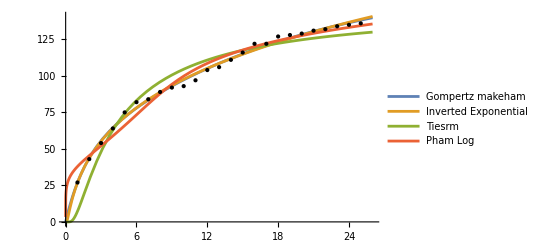

```mathematica
Plot[{gm[t],invertedExponential[t],tiesrm[t],phamLog[t]},{t,0,26},Epilog->Point[dataWeek3],PlotStyle->{"Red","Purple","Green","Blue"},PlotLegends->{"Gompertz makeham", "Inverted Exponential","Tiesrm","Pham Log"}]
```

```mathematica
Grid[{#,gm[#],invertedExponential[#],tiesrm[#],phamLog[#]}&[{"AIC","BIC","RSquared","AdjustedRSquared"}], Frame->All]
```

AIC | BIC | RSquared | AdjustedRSquared
120.739 | 126.833 | 0.999567 | 0.999484
121.724 | 126.599 | 0.999509 | 0.999442
180.116 | 184.992 | 0.994922 | 0.994229
158.257 | 164.351 | 0.998057 | 0.997687

На базата на статистическите тестове най- добри стойности получаваме за Gompertz Makeham.